# 1.3 Degenerate Linear System

### Part a)

```mathematica
s = 1
```

1

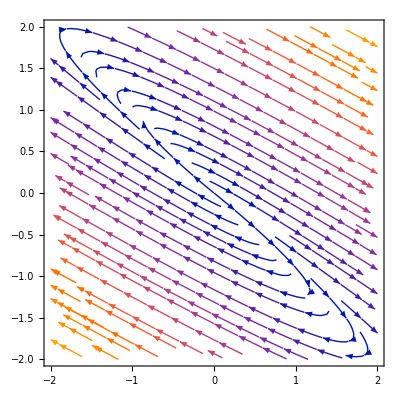

```mathematica
p1 = StreamPlot[{(s+3)*x+4*y, -9/4*x+(s-3)*y },
 {x,-2 , 2},{y ,-2, 2}]
```

```mathematica
minx = -2;
miny = -2;
maxx = 2;
maxy = 2;
z = 1.5
```

1.5

```mathematica
sol[x0_ , y0_] :=NDSolve[
{x'[t]== (s+3)*x[t]+4*y [t], 
y'[t] == -9/4*x[t]+(s-3)*y[t], x[0] == x0 , y[0] == y0} 
, {x,y} , {t,-3,3}]
```

```mathematica
dz = 0.7
```

0.7

```mathematica
initialC=Tuples[{Range[-z,z,dz],Range[-z,z,dz]}]
```

{{-1.5,-1.5},{-1.5,-0.8},{-1.5,-0.1},{-1.5,0.6},{-1.5,1.3},{-0.8,-1.5},{-0.8,-0.8},{-0.8,-0.1},{-0.8,0.6},{-0.8,1.3},{-0.1,-1.5},{-0.1,-0.8},{-0.1,-0.1},{-0.1,0.6},{-0.1,1.3},{0.6,-1.5},{0.6,-0.8},{0.6,-0.1},{0.6,0.6},{0.6,1.3},{1.3,-1.5},{1.3,-0.8},{1.3,-0.1},{1.3,0.6},{1.3,1.3}}

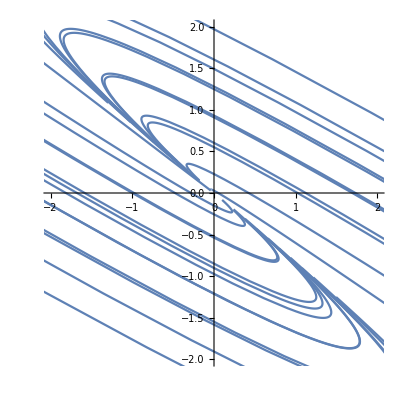

```mathematica
p2 = Show[
Table[
ParametricPlot[
Evaluate[{x[t] , y[t]}/. sol[initialC[[i,1]] , initialC[[i,2]]]]
,{t,-3,3} , PlotRange->{{-2,2} , {-2,2}}],
{i,1,Length[initialC]}]/. Line[x_] :> {Arrowheads[{0.035,0.07,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0} ], Arrow[x]}
]
```

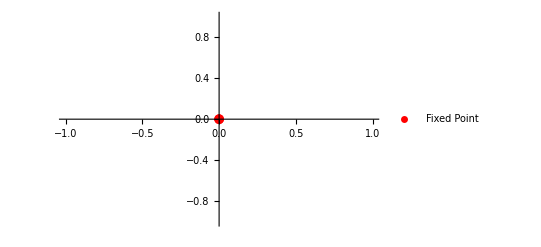

```mathematica
p3 = ListPlot[{{0,0}}, PlotMarkers->{Automatic,10}, PlotStyle -> Red,PlotLegends->{"Fixed Point"} ]
```

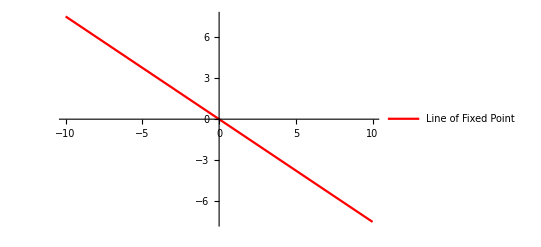

```mathematica
p4 = Plot[-3/4*x, {x,-10,10}, PlotStyle -> Red,PlotLegends->{"Line of Fixed Point"} ]
```

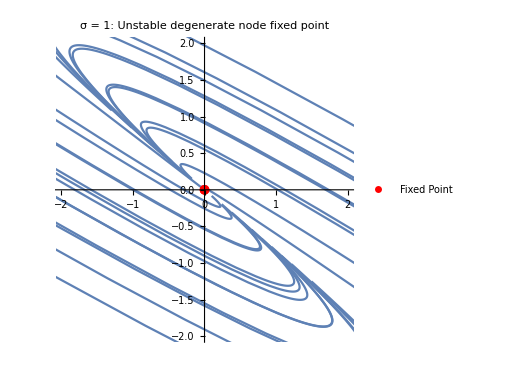

```mathematica
Show[p2,p3, PlotLabel-> "σ = 1: Unstable degenerate node fixed point"]
```

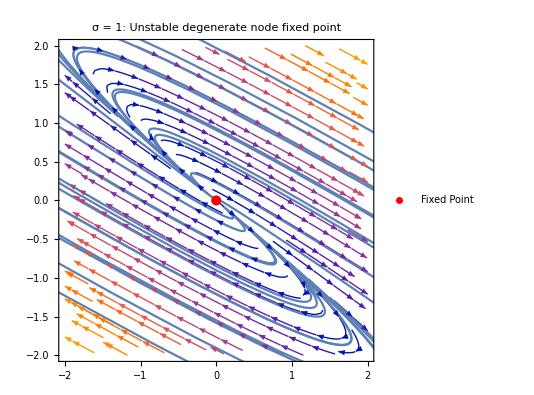

```mathematica
Show[p1,p2,p3, PlotLabel-> "σ = 1: Unstable degenerate node fixed point"]
```

### Part b)

```mathematica
M = {{σ+3,4},{-9/4,σ-3}}
```

{{3+σ,4},{-9/4,-3+σ}}

```mathematica
MatrixForm[M]
```

(3+σ | 4
-9/4 | -3+σ)

```mathematica
eigen = Eigensystem[M]
```

{{σ,σ},{{-4/3,1},{0,0}}}

So the eigenvalues are {σ, σ} and eigenvector {-4/3, 1}

### Part c)

```mathematica
v = Normalize[eigen[[2,1]]]
```

{-4/5,3/5}

So the normed eigenvector with positive x component is {4/5, -3/5}

### Part d)

```mathematica
Inverse[M]
```

{{(-3+σ)/σ^2,-4/σ^2},{9/(4 σ^2),(3+σ)/σ^2}}

```mathematica
MatrixForm[{{(-3+σ)/σ^2,-4/σ^2},{9/(4 σ^2),(3+σ)/σ^2}}]
```

((-3+σ)/σ^2 | -4/σ^2
9/(4 σ^2) | (3+σ)/σ^2)

### Part e)

```mathematica
Det[M]
```

σ^2

So M is singular iff Det[M] == 0 iff σ = 0

### Part f)

```mathematica
K = {{σ-c*d, d^2},{-c^2, (σ+c*d)}}
```

{{-c d+σ,d^2},{-c^2,c d+σ}}

```mathematica
MatrixForm[K]
```

(-c d+σ | d^2
-c^2 | c d+σ)

```mathematica
Solve[K == M, {c,d}, Assumptions->c>0]
```

{{c→3/2,d→-2}}

So c = 3/2 and d = -2

### Part g)

```mathematica
Eigenvalues[K]
```

{σ,σ}

So the eigenvalues are both equal to σ

### Part h)

```mathematica
w = Eigenvectors[K]
```

{{d/c,1},{0,0}}

```mathematica
w1 = w[[1]]
```

{d/c,1}

```mathematica
Normalize[w1]//Expand
```

{d/(c √(1+Abs[d/c]^2)),1/(√(1+Abs[d/c]^2))}

So the normed eigenvector (which corresponds to the stable direction for σ = -1, the unstable direction for σ = 1 and the line of fixed points for σ = 0) equals {d/Sqrt[c^2 + d^2], c/Sqrt[c^2 + d^2]}